#### Hamiltonian Diagonalization

```mathematica
ClearAll["Global`*"]

n=14;(*Lx*)
n1=12;(*Ly*)
rightpt=1;(* magnetic field upper bond, 1->2pi *)
gaugeox=0.;(* gauge origin in the x direction, when =0, set to Lx/2 *)
ox=0.;(* origin in resta's formula, when =0, set to Lx *)
δ=0.07;(* chemical potential increment *)

(* initialize graph *)
g=GridGraph[{n,n1},VertexLabels->Automatic];
adj=AdjacencyMatrix[g];
zeros=Table[0,{i,Length[adj]},{j,Length[adj]}];
gaugechoice=zeros;
ones=Table[1,{i,Length[adj]},{j,Length[adj]}];
adjg=AdjacencyGraph[adj];
indexT= Table[VertexList[g][[i]]->i,{i,1,Length[VertexList[g]]}];
zerolist=Table[0,{i,Length[adj]}];

path=Table[FindShortestPath[g,i,i+n*n1-n],{i,1,n}];
path2=Table[FindShortestPath[g,1+n*i,n+n*i],{i,0,n1-1}];
(*
HighlightGraph[g,path]
HighlightGraph[g,path2]
*)
(* define \hat{P} in Resta's formula *)

alist=Table[path[[i]][[1;;-1]],{i,Length[path]}];
arules=Table[Thread[alist[[i]]->Exp[I*2Pi*(i-ox)/n]],{i,Length[alist]}]//Flatten;

xlist=ReplacePart[zerolist,arules];
py=DiagonalMatrix[xlist];

(* Hamiltonian *)
(* connecting boundaries to make torus *)
replace=Flatten[Table[{(path[[i,j]]),(path[[i,Mod[j+1,n1,1]]])}->1,{i,Length[path]},{j,Length[path[[i]]]}]];
replace2=Flatten[Table[{(path[[i,Mod[j+1,n1,1]]]),(path[[i,j]])}->1,{i,Length[path]},{j,Length[path[[i]]]}]];
replace3=Flatten[Table[{(path2[[i,j]]),(path2[[i,Mod[j+1,n,1]]])}->1,{i,Length[path2]},{j,Length[path2[[i]]]}]];
replace4=Flatten[Table[{(path2[[i,Mod[j+1,n,1]]]),(path2[[i,j]])}->1,{i,Length[path2]},{j,Length[path2[[i]]]}]];

disLH=adj;

disLH=ReplacePart[disLH,replace];
disLH=ReplacePart[disLH,replace2];
disLH=ReplacePart[disLH,replace3]; 
disLH=ReplacePart[disLH,replace4];


(* now add flux *)
(* path 2 along y direction, path along x direction*)
add=2Pi/(n*n1)*numofflux;(*\phi*)
bdd=add*(n1);


(*y direction vector potential (changing gauge origin in this direction does nothing) *)

addlist=Flatten[Table[{(path2[[i,j]]/.indexT),(path2[[i,Mod[j+1,n,1]]]/.indexT)}->(i)*add*I,{i,Length[path2]},{j,Length[path2[[i]]]}]];


(* x direction vector potentia with variable gauge origin *)
bddlist=Flatten[Table[{(path[[i,-1]]),(path[[i,1]])}->-(i-n/2-gaugeox)*bdd*I,{i,Length[path]}]];


addmat=ReplacePart[zeros,addlist];
bddmat=ReplacePart[zeros,bddlist];

gaugechoice+=addmat;
gaugechoice+=bddmat;

gaugechoice+=ConjugateTranspose[gaugechoice];


disLH=-Table[disLH[[i]][[j]]*Exp[gaugechoice[[i]][[j]]],{i,Length[adj]},{j,Length[adj]}];



slaterCon[psi1_,psi2_]:=If[psi1=={}||psi2=={},1,Det[Table[Conjugate[psi1[[i]]].psi2[[j]],{i,Length[psi1]},{j,Length[psi2]}]]];

savedlowerband={};
savedphase=0;

(* iterate over magnetic field *)
chargeTab=ParallelTable[

numofflux=iterA;
{val1,vec1}=Eigensystem[N[disLH]/.numofflux->iterA];

(* iterate over chemical potential *)
phaseoutput=Table[
lowerbandid=Position[val1,n_ /;-4<n<=iterB]//Flatten;

lowerband=Join[Table[vec1[[lowerbandid[[i]]]] ,{i,Length[lowerbandid]}]];

If[lowerband!=savedlowerband,
phase1=TimeConstrained[Arg[slaterCon[lowerband,If[lowerband=={},{},Transpose[py.Transpose[lowerband]]]]]/(2Pi),20,1];
savedphase=phase1;
,
phase1=savedphase;
];


savedlowerband=lowerband;
phase1
,{iterB,-4,4,δ}]

,{iterA,0,(n*n1)*rightpt,1}];
```

#### Plotting

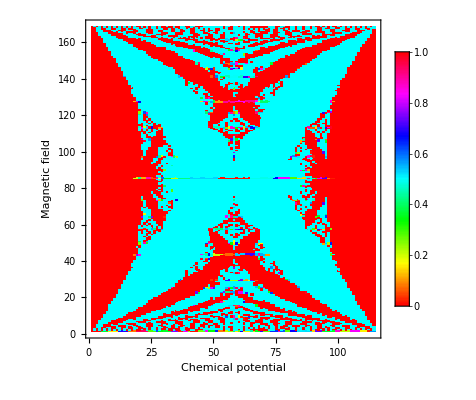

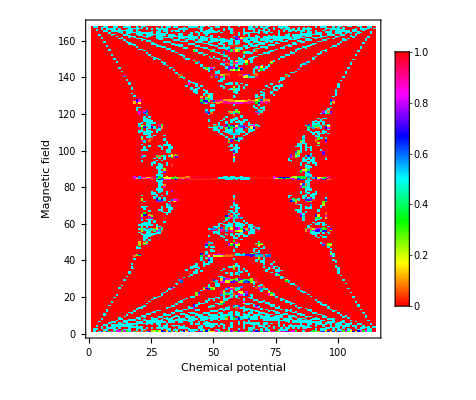

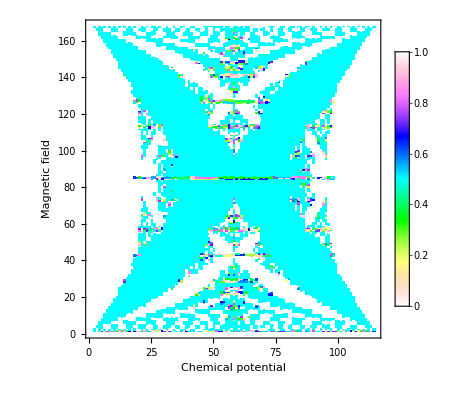

```mathematica
CoolColor[ z_ ] :=Hue[z,If[z<0.5,3z,3-3z],1];

(*\mathcal{P} mod 1*)
fracC1=Chop[Mod[N[chargeTab],1]];

(*linear in \phi contribution of \mathcal{P}*)
difrac=Mod[Drop[fracC1,1]-Drop[fracC1,-1],1];

(*constant contribution of \mathcal{P}*)
pol=Mod[Table[fracC1[[i]]-difrac[[i]]*i,{i,Length[difrac]}],1];

ListDensityPlot[fracC1,ColorFunction->Function[z,Hue[z*4/4]],PlotLegends->Automatic,FrameLabel->{"Chemical potential","Magnetic field"},InterpolationOrder->0]
ListDensityPlot[difrac,ColorFunction->Function[z,Hue[z*4/4]],PlotLegends->Automatic,FrameLabel->{"Chemical potential","Magnetic field"},InterpolationOrder->0]
ListDensityPlot[pol,ColorFunction->CoolColor,PlotLegends->Automatic,FrameLabel->{"Chemical potential","Magnetic field"},InterpolationOrder->0]
```